```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L:=10
(*Number of Time Steps:*)
n:=10
(*Distance between instanton and anti-instanton*)
R:=5
(*Distance between quark and anti-quark*)
r:=1
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Define instanton solutions
Areg[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)
Aanti[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)*)
```

```mathematica
(*Instanton rotation*)
Rvec:=R{Sin[θ3]Sin[θ2]Sin[θ1],Sin[θ3]Sin[θ2]Cos[θ1],Sin[θ3]Cos[θ2],Cos[θ3]}
Simplify[Sum[Rvec[[m]]^2,{m,1,4}]]
```

25

```mathematica
(*Ratio Ansatz*)
Ya[y_]:=y+Rvec/2
Yi[y_]:=y-Rvec/2
Arat[y_]:=Table[Sum[(ηbar[[μ,ν,aa]]*Yi[y][[ν]]*Ya[y].Ya[y]+η[[μ,ν,aa]]*Ya[y][[ν]]*Yi[y].Yi[y])/((Yi[y].Yi[y])(Ya[y].Ya[y])+Yi[y].Yi[y]+Ya[y].Ya[y]),{ν,1,4}],{μ,1,4},{aa,1,3}]
```

```mathematica
(*Wilson Line at a point in time, d stands for dagger *)
W2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]]+I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]]
Wd2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]]-I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]]
```

```mathematica
(*Table of wilson lines along L*)
WList[y_]:=Table[W2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,1,n}]
WdList[y_]:=Table[Wd2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,1,n}]
```

```mathematica
(*Matrix Product*)
Wapprox[y_]:=Dot@@WList[y] (* applies the function to everything in the table *)
Wdapprox[y_]:=Dot@@WdList[y]
ypoint={1.,1.,0.,0};
Mexample=Wapprox[ypoint]/.{θ3->0,θ1->0,θ2->0} (* just example *)
```

{{0.048392+1.52974×10^-17 ⅈ,0.706278+0.706278 ⅈ},{-0.706278+0.706278 ⅈ,0.048392-1.52974×10^-17 ⅈ}}

```mathematica
Tr[Mexample.ConjugateTranspose[Mexample]]
```

2.+0. ⅈ

```mathematica
Mexample // MatrixForm
```

(0.048392+1.52974×10^-17 ⅈ | 0.706278+0.706278 ⅈ
-0.706278+0.706278 ⅈ | 0.048392-1.52974×10^-17 ⅈ)

```mathematica
Igd[y_]:=1-Tr[Wapprox[y].Wdapprox[y-{r*1.,0,0,0}]]/2(* integrand *) 
Igd[ypoint]/.{θ3->1.,θ1->0,θ2->0,y1->.1,y2->0,y3->0,y4->-1.}
```

0.0144415+0. ⅈ

```mathematica
Igd[ypoint]/.{θ3->1.,θ1->0,θ2->0,y1->.1,y2->0,y3->0,y4->0}
```

0.0144415+0. ⅈ

```mathematica
Plot[Re[Igd[ypoint]/.{θ3->1.,θ1->0,θ2->0,y1->.1,y2->0,y3->0}],{y4,-5,5}]
```

$Aborted

```mathematica
Igd[ypoint]/.{θ3->0,θ1->0,θ2->0}
```

0.707479+0. ⅈ

```mathematica
Igd[ypoint]/.{θ3->1.,θ1->0,θ2->0}
```

0.985559+0. ⅈ

```mathematica
AngleData=Table[{θ3,NIntegrate[Sin[θ3]^2Sin[θ2]Igd[{y1,y2,y3,0}],{θ1,0,2Pi},{θ2,0,Pi},{y1,-10,10},{y2,-10,10},{y3,-10,10},AccuracyGoal->2]},{θ3,0,Pi,Pi/10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9560.52-7.23993×10^-18 ⅈ and 0.02558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 34553.1+3.01249×10^-16 ⅈ and 0.239417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 65385.4-4.38894×10^-17 ⅈ and 0.931527 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{0,0.},{π/10,9560.52},{π/5,34553.1},{(3 π)/10,65385.4},{(2 π)/5,90244.},{π/2,99700.8},{(3 π)/5,90244.},{(7 π)/10,65385.4},{(4 π)/5,34553.1},{(9 π)/10,9560.52},{π,0.}}

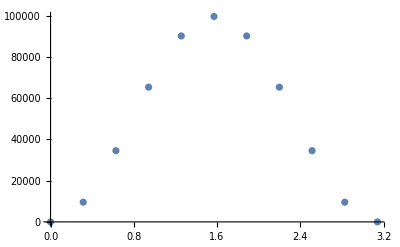

```mathematica
ListPlot[Re[AngleData]]
```

```mathematica
Table[{θ3,NIntegrate[Sin[θ3]^2Sin[θ2]Igd[{y1,y2,y3,0}],{θ1,0,2Pi},{θ2,0,Pi},{y1,-100,100},{y2,-100,100},{y3,-100,100}]},{θ3,Pi/2-0.1,Pi/2+0.1,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -12.3431+1.40177×10^-14 ⅈ and 26.6154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00421083+4.30768×10^-14 ⅈ and 31.03 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.3431+2.91216×10^-15 ⅈ and 26.6154 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{1.4708,-12.3431+1.40177×10^-14 ⅈ},{1.5708,-0.00421083+4.30768×10^-14 ⅈ},{1.6708,12.3431}}